```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/StocForm_for_Gauge/num"]
```

/Users/yuichirotada/Documents/Univ/StocForm_for_Gauge/num

```mathematica
ep={Cos[ϕ]Cos[θ]-I Sin[ϕ],Sin[ϕ]Cos[θ]+I Cos[ϕ],-Sin[θ]};
em={Cos[ϕ]Cos[θ]+I Sin[ϕ],Sin[ϕ]Cos[θ]-I Cos[ϕ],-Sin[θ]};
kk=k{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
ep.em//Simplify
kk.ep//Simplify
kk.em//Simplify
(I kk×ep).em/2//Simplify
(I kk×em).ep/2//Simplify
```

2

0

0

k

-k

```mathematica
kappa=1/50;
xi=5;
HH=10^-5;
```

```mathematica
WW[z_]=WhittakerW[-I xi,1/2,-2I z];
```

```mathematica
Amp=(kappa^4 HH^4)/(12 π^2)E^(π xi)(Abs[WW[kappa]]^2+Abs[WW'[kappa]]^2);
RR=1/Sqrt[Abs[WW[kappa]]^2+Abs[WW'[kappa]]^2]{{Abs[WW'[kappa]],Abs[WW[kappa]]},{-Abs[WW[kappa]],Abs[WW'[kappa]]}};
RT=Transpose[RR];
```

```mathematica
RR.{{Abs[WW[kappa]]^2,-Abs[WW[kappa]]Abs[WW'[kappa]]},{-Abs[WW[kappa]]Abs[WW'[kappa]],Abs[WW'[kappa]]^2}}.RT//Simplify//MatrixForm
```

(0 | 0
0 | Abs[WhittakerW[-5 ⅈ,1/2,-ⅈ/25]]^2+4 Abs[249/2 WhittakerW[-5 ⅈ,1/2,-ⅈ/25]+25 ⅈ WhittakerW[1-5 ⅈ,1/2,-ⅈ/25]]^2)

```mathematica
SDE={ⅆBx[NN]+2Bx[NN]ⅆNN==RT[[1,2]]Sqrt[Amp]ⅆWx[NN],
ⅆBy[NN]+2By[NN]ⅆNN==RT[[1,2]]Sqrt[Amp]ⅆWy[NN],
ⅆBz[NN]+2Bz[NN]ⅆNN==RT[[1,2]]Sqrt[Amp]ⅆWz[NN],
ⅆEx[NN]+2Ex[NN]ⅆNN+2xi Bx[NN]ⅆNN==RT[[2,2]]Sqrt[Amp]ⅆWx[NN],ⅆEy[NN]+2Ey[NN]ⅆNN+2xi By[NN]ⅆNN==RT[[2,2]]Sqrt[Amp]ⅆWy[NN],
ⅆEz[NN]+2Ez[NN]ⅆNN+2xi Bz[NN]ⅆNN==RT[[2,2]]Sqrt[Amp]ⅆWz[NN]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[NN],By[NN],Bz[NN],Ex[NN],Ey[NN],Ez[NN]},{{Bx,By,Bz,Ex,Ey,Ez},{0,0,0,0,0,0}},NN,{Wx\[Distributed]WienerProcess[],Wy\[Distributed]WienerProcess[],Wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
real=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

{144.319,Null}

```mathematica
realtmp=real
```

TemporalData[…]

```mathematica
Export["EBrealization.wdx",real];
```

```mathematica
real=Import["EBrealization.wdx"];
```

```mathematica
Breal[NN_]={real["PathComponent",1]["PathFunction"][NN],
real["PathComponent",2]["PathFunction"][NN],
real["PathComponent",3]["PathFunction"][NN]};
Ereal[NN_]={real["PathComponent",4]["PathFunction"][NN],
real["PathComponent",5]["PathFunction"][NN],
real["PathComponent",6]["PathFunction"][NN]};
```

```mathematica
BAmp[NN_]=Norm[Breal[NN]]^2;
NormB[NN_]=Breal[NN]/Norm[Breal[NN]];
EAmp[NN_]=Norm[Ereal[NN]]^2;
NormE[NN_]=Ereal[NN]/Norm[Ereal[NN]];
rhoIR[NN_]=(BAmp[NN]+EAmp[NN])/2;
```

```mathematica
calPBB[z_]=(z^4 HH^4)/(4 π^2)E^(π xi)Abs[WW[z]]^2;
calPEE[z_]=(z^4 HH^4)/(4 π^2)E^(π xi)Abs[WW'[z]]^2;
calPBE[z_]=(z^4 HH^4)/(4 π^2)E^(π xi)WW[z]Conjugate[WW'[z]];
```

```mathematica
varB=1/4 calPBB[kappa];
varE=1/4 calPEE[kappa]-xi/8 Re[calPBE[kappa]]+xi^2/8 calPBB[kappa];
sigmaB=Sqrt[2/3]varB;
sigmaE=Sqrt[2/3]varE;
rhoexp=(varB+varE)/2;
sigmarho=Sqrt[2/3]rhoexp;
```

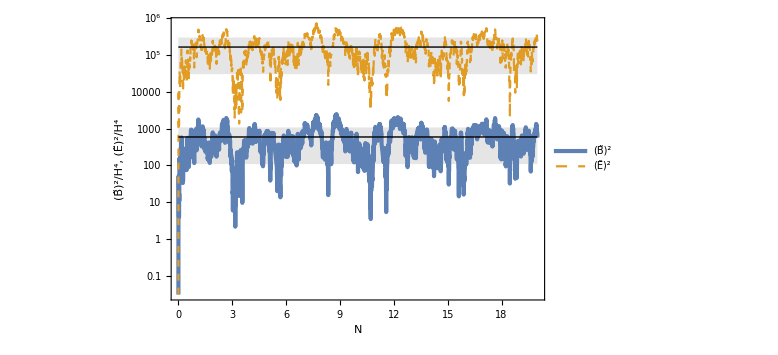

```mathematica
FigE2B2=LogPlot[{BAmp[NN]/HH^4,EAmp[NN]/HH^4,varB/HH^4,(varB+sigmaB)/HH^4,(varB-sigmaB)/HH^4,varE/HH^4,(varE+sigmaE)/HH^4,(varE-sigmaE)/HH^4},{NN,0,Nf},PlotStyle->{AbsoluteThickness[3],Dashed,{Black,Thin},None,None,{Black,Thin},None,None},Filling->{{4->{5}},7->{8}},FillingStyle->Directive[Gray,Opacity[0.2]],FrameLabel->{N,Row[{OverTilde[Style["B",Italic,Bold]]^2,"/",H^4,",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",H^4}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

```mathematica
Export["BAmpEAmp_err.pdf",FigE2B2];
```

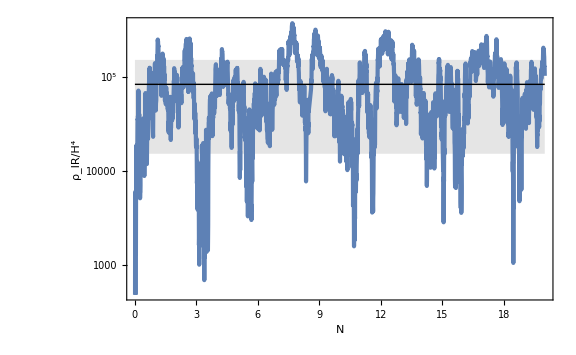

```mathematica
Figrho=LogPlot[{HH^-4 rhoIR[NN],HH^-4 rhoexp,HH^-4(rhoexp+sigmarho),HH^-4(rhoexp-sigmarho)},{NN,0,Nf},PlotStyle->{AbsoluteThickness[3],{Black,Thin},None,None},Filling->{3->{4}},FillingStyle->Directive[Gray,Opacity[0.2]],FrameLabel->{N,Row[{Subscript[ρ, IR],"/",H^4}]}]
```

```mathematica
Export["rhoIR.pdf",Figrho];
```

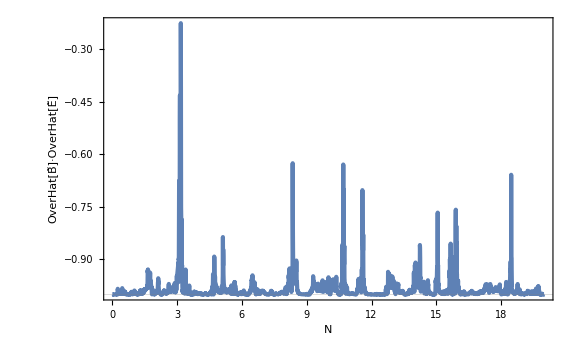

```mathematica
FigEdotB=Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{-1}}]
```

```mathematica
Export["EdotB.pdf",FigEdotB];
```

```mathematica
vp={1.3,-2.4,2.};
θv=ArcTan[vp[[3]],Sqrt[vp[[1]]^2+vp[[2]]^2]]
ϕv=ArcTan[vp[[1]],vp[[2]]]
θax=π/2-θv
ϕax=ϕv+π
Rθv={{Cos[θv],0,Sin[θv]},{0,1,0},{-Sin[θv],0,Cos[θv]}};
Rϕv={{Cos[ϕv],-Sin[ϕv],0},{Sin[ϕv],Cos[ϕv],0},{0,0,1}};
Rθax={{Cos[θax],0,Sin[θax]},{0,1,0},{-Sin[θax],0,Cos[θax]}};
Rϕax={{Cos[ϕax],-Sin[ϕax],0},{Sin[ϕax],Cos[ϕax],0},{0,0,1}};
Rϕ[ϕ_]={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
vax={Sin[θax]Cos[ϕax],Sin[θax]Sin[ϕax],Cos[θax]}
vax.vp
```

0.938431

-1.07437

0.632365

2.06722

{{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}

{-0.281509,0.519709,0.806632}

2.22045×10^-16

```mathematica
Transpose[Rθax].Transpose[Rϕax].vax
```

{0.,0.,1.}

```mathematica
Nplot=9;
Manipulate[Show[ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Gray,Opacity[0.01]],MeshStyle->Dotted,Boxed->False,Axes->None],
ParametricPlot3D[{Rϕ[-ϕvp].NormB[NN],Rϕ[-ϕvp].NormE[NN]},{NN,Nplot-dN/2,Nplot+dN/2}]],{ϕvp,0,π},{dN,{0.1,0.5,2,10}}]
```

```mathematica
FigDirection=Table[Show[ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotStyle->Directive[Gray,Opacity[0.01]],MeshStyle->Dotted,Boxed->False,Axes->None],
ParametricPlot3D[{NormB[NN],NormE[NN]},{NN,Nplot-dN/2,Nplot+dN/2},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]]],{dN,{0.1,0.5,2,10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["3D01_sph.pdf",FigDirection[[1]]];
Export["3D05_sph.pdf",FigDirection[[2]]];
Export["3D2_sph.pdf",FigDirection[[3]]];
Export["3D10_sph.pdf",FigDirection[[4]]];
```